Taylor expansions

```mathematica
θ[τ_]:=ϵ θ1[τ]+ϵ^2 θ2[τ]+ϵ^3 θ3[τ];
g=g0+ϵ^2 g2;
H[x_]:=h1 x +  h3 x^3;
```

Left hand side of the phase equation:

```mathematica
μ D[θ[τ],τ]
```

μ (ϵ θ1'[τ]+ϵ^2 θ2'[τ]+ϵ^3 θ3'[τ])

Right hand side of the phase equation. collect in terms of order epsilon. The triple I represents the integral. We write integrals this way so it is easier to collect integral terms later on.

```mathematica
(* RHS *)
Collect[-q H[θ[τ]]- β g III Exp[-β s] H[θ[τ-s]-θ[τ]],ϵ]
```

ϵ (-h1 q θ1[τ]+ⅇ^(-s β) g0 h1 III β θ1[τ]-ⅇ^(-s β) g0 h1 III β θ1[-s+τ])+ϵ^2 (-h1 q θ2[τ]+ⅇ^(-s β) g0 h1 III β θ2[τ]-ⅇ^(-s β) g0 h1 III β θ2[-s+τ])+ϵ^4 (ⅇ^(-s β) g2 h1 III β θ2[τ]-3 h3 q θ1[τ]^2 θ2[τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ2[τ]-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ] θ2[τ]+3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^2 θ2[τ]-ⅇ^(-s β) g2 h1 III β θ2[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ2[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ] θ2[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^2 θ2[-s+τ])+ϵ^3 (ⅇ^(-s β) g2 h1 III β θ1[τ]-h3 q θ1[τ]^3+ⅇ^(-s β) g0 h3 III β θ1[τ]^3-ⅇ^(-s β) g2 h1 III β θ1[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ1[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^3-h1 q θ3[τ]+ⅇ^(-s β) g0 h1 III β θ3[τ]-ⅇ^(-s β) g0 h1 III β θ3[-s+τ])+ϵ^5 (ⅇ^(-s β) g2 h3 III β θ1[τ]^3-3 ⅇ^(-s β) g2 h3 III β θ1[τ]^2 θ1[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ1[τ] θ1[-s+τ]^2-ⅇ^(-s β) g2 h3 III β θ1[-s+τ]^3-3 h3 q θ1[τ] θ2[τ]^2+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[τ]^2-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[τ]^2-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[τ] θ2[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[τ] θ2[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[-s+τ]^2-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[-s+τ]^2+ⅇ^(-s β) g2 h1 III β θ3[τ]-3 h3 q θ1[τ]^2 θ3[τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ3[τ]-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ] θ3[τ]+3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^2 θ3[τ]-ⅇ^(-s β) g2 h1 III β θ3[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ] θ3[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^2 θ3[-s+τ])+ϵ^6 (3 ⅇ^(-s β) g2 h3 III β θ1[τ]^2 θ2[τ]-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ1[-s+τ] θ2[τ]+3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ]^2 θ2[τ]-h3 q θ2[τ]^3+ⅇ^(-s β) g0 h3 III β θ2[τ]^3-3 ⅇ^(-s β) g2 h3 III β θ1[τ]^2 θ2[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ1[-s+τ] θ2[-s+τ]-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ]^2 θ2[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ2[τ]^2 θ2[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ2[τ] θ2[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ2[-s+τ]^3-6 h3 q θ1[τ] θ2[τ] θ3[τ]+6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[τ] θ3[τ]-6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[τ] θ3[τ]-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[-s+τ] θ3[τ]+6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[-s+τ] θ3[τ]-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[τ] θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[τ] θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ2[-s+τ] θ3[-s+τ]-6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ2[-s+τ] θ3[-s+τ])+ϵ^7 (3 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[τ]^2-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[τ]^2-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[τ] θ2[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[τ] θ2[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[-s+τ]^2-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[-s+τ]^2+3 ⅇ^(-s β) g2 h3 III β θ1[τ]^2 θ3[τ]-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ1[-s+τ] θ3[τ]+3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ]^2 θ3[τ]-3 h3 q θ2[τ]^2 θ3[τ]+3 ⅇ^(-s β) g0 h3 III β θ2[τ]^2 θ3[τ]-6 ⅇ^(-s β) g0 h3 III β θ2[τ] θ2[-s+τ] θ3[τ]+3 ⅇ^(-s β) g0 h3 III β θ2[-s+τ]^2 θ3[τ]-3 h3 q θ1[τ] θ3[τ]^2+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ3[τ]^2-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ3[τ]^2-3 ⅇ^(-s β) g2 h3 III β θ1[τ]^2 θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ1[-s+τ] θ3[-s+τ]-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ]^2 θ3[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ2[τ]^2 θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ2[τ] θ2[-s+τ] θ3[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ2[-s+τ]^2 θ3[-s+τ]-6 ⅇ^(-s β) g0 h3 III β θ1[τ] θ3[τ] θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ3[τ] θ3[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ3[-s+τ]^2-3 ⅇ^(-s β) g0 h3 III β θ1[-s+τ] θ3[-s+τ]^2)+ϵ^8 (ⅇ^(-s β) g2 h3 III β θ2[τ]^3-3 ⅇ^(-s β) g2 h3 III β θ2[τ]^2 θ2[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ2[τ] θ2[-s+τ]^2-ⅇ^(-s β) g2 h3 III β θ2[-s+τ]^3+6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[τ] θ3[τ]-6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[τ] θ3[τ]-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[-s+τ] θ3[τ]+6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[-s+τ] θ3[τ]-3 h3 q θ2[τ] θ3[τ]^2+3 ⅇ^(-s β) g0 h3 III β θ2[τ] θ3[τ]^2-3 ⅇ^(-s β) g0 h3 III β θ2[-s+τ] θ3[τ]^2-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[τ] θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[τ] θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ2[-s+τ] θ3[-s+τ]-6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ2[-s+τ] θ3[-s+τ]-6 ⅇ^(-s β) g0 h3 III β θ2[τ] θ3[τ] θ3[-s+τ]+6 ⅇ^(-s β) g0 h3 III β θ2[-s+τ] θ3[τ] θ3[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ2[τ] θ3[-s+τ]^2-3 ⅇ^(-s β) g0 h3 III β θ2[-s+τ] θ3[-s+τ]^2)+ϵ^10 (3 ⅇ^(-s β) g2 h3 III β θ2[τ] θ3[τ]^2-3 ⅇ^(-s β) g2 h3 III β θ2[-s+τ] θ3[τ]^2-6 ⅇ^(-s β) g2 h3 III β θ2[τ] θ3[τ] θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ2[-s+τ] θ3[τ] θ3[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ2[τ] θ3[-s+τ]^2-3 ⅇ^(-s β) g2 h3 III β θ2[-s+τ] θ3[-s+τ]^2)+ϵ^9 (3 ⅇ^(-s β) g2 h3 III β θ2[τ]^2 θ3[τ]-6 ⅇ^(-s β) g2 h3 III β θ2[τ] θ2[-s+τ] θ3[τ]+3 ⅇ^(-s β) g2 h3 III β θ2[-s+τ]^2 θ3[τ]+3 ⅇ^(-s β) g2 h3 III β θ1[τ] θ3[τ]^2-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ3[τ]^2-h3 q θ3[τ]^3+ⅇ^(-s β) g0 h3 III β θ3[τ]^3-3 ⅇ^(-s β) g2 h3 III β θ2[τ]^2 θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ2[τ] θ2[-s+τ] θ3[-s+τ]-3 ⅇ^(-s β) g2 h3 III β θ2[-s+τ]^2 θ3[-s+τ]-6 ⅇ^(-s β) g2 h3 III β θ1[τ] θ3[τ] θ3[-s+τ]+6 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ3[τ] θ3[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ3[τ]^2 θ3[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ1[τ] θ3[-s+τ]^2-3 ⅇ^(-s β) g2 h3 III β θ1[-s+τ] θ3[-s+τ]^2+3 ⅇ^(-s β) g0 h3 III β θ3[τ] θ3[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ3[-s+τ]^3)+ϵ^11 (ⅇ^(-s β) g2 h3 III β θ3[τ]^3-3 ⅇ^(-s β) g2 h3 III β θ3[τ]^2 θ3[-s+τ]+3 ⅇ^(-s β) g2 h3 III β θ3[τ] θ3[-s+τ]^2-ⅇ^(-s β) g2 h3 III β θ3[-s+τ]^3)

Copy/paste terms of order ϵ^3, then collect the θ_3 terms to isolate the terms on the right hand side of the linear map.

```mathematica
Collect[ⅇ^(-s β) g2 h1 III β θ1[τ]-h3 q θ1[τ]^3+ⅇ^(-s β) g0 h3 III β θ1[τ]^3-ⅇ^(-s β) g2 h1 III β θ1[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ1[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^3-h1 q θ3[τ]+ⅇ^(-s β) g0 h1 III β θ3[τ]-ⅇ^(-s β) g0 h1 III β θ3[-s+τ],θ3]
```

ⅇ^(-s β) g2 h1 III β θ1[τ]-h3 q θ1[τ]^3+ⅇ^(-s β) g0 h3 III β θ1[τ]^3-ⅇ^(-s β) g2 h1 III β θ1[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ1[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^3-h1 q θ3[τ]+ⅇ^(-s β) g0 h1 III β θ3[τ]-ⅇ^(-s β) g0 h1 III β θ3[-s+τ]

Copy/paste the θ_3 terms above and rewrite in linear map form (sanity check)

```mathematica
FullSimplify[Collect[-h1 q θ3[τ]+ⅇ^(-s β) g0 h1 III β θ3[τ]-ⅇ^(-s β) g0 h1 III β θ3[-s+τ],III]]
```

-h1 q θ3[τ]+ⅇ^(-s β) g0 h1 III β (θ3[τ]-θ3[-s+τ])

copy/paste the remaining terms above, whish is the RHS of the linear map. Collect the integral terms together.

```mathematica
Collect[FullSimplify[ⅇ^(-s β) g2 h1 III β θ1[τ]-h3 q θ1[τ]^3+ⅇ^(-s β) g0 h3 III β θ1[τ]^3-ⅇ^(-s β) g2 h1 III β θ1[-s+τ]-3 ⅇ^(-s β) g0 h3 III β θ1[τ]^2 θ1[-s+τ]+3 ⅇ^(-s β) g0 h3 III β θ1[τ] θ1[-s+τ]^2-ⅇ^(-s β) g0 h3 III β θ1[-s+τ]^3],III]
```

-h3 q θ1[τ]^3+ⅇ^(-s β) III β (g2 h1+g0 h3 (θ1[τ]-θ1[-s+τ])^2) (θ1[τ]-θ1[-s+τ])

Now that we have the right hand side, we look for bounded periodic solutions θ_3 by applying the orthogonality condition from the Fredholm Alternative. The following calculation is the inner product of the right hand side of the order ϵ^3 linear map with the function in the nullspace of the adjoint of the linear map.

```mathematica
th1[t_] := z Exp[I ω t]+Conjugate[z] Exp[-I ω t];
```

```mathematica
FullSimplify[Integrate[(-q h3 th1[t]^3 - β g0 h3 Integrate[Exp[-β s](th1[t-s]-th1[t])^3,{s,0,Infinity}]- β g2 h1 Integrate[Exp[-β s](th1[t-s]-th1[t]),{s,0,Infinity}])th1[t],{t,0,T}]/.T->2Pi/ω]
```

ConditionalExpression[(4 π z Conjugate[z] (g2 h1 ω^2 (β^2+4 ω^2)-3 h3 z (-12 g0 ω^4+q (β^2+ω^2) (β^2+4 ω^2)) Conjugate[z]))/(ω (β^2+ω^2) (β^2+4 ω^2)),3 Im[ω]<Re[β]&&3 Im[ω]+Re[β]>0]

Simplify the expression and separate the real and imaginary components

```mathematica
FullSimplify[ComplexExpand[(4 π z Conjugate[z] (g2 h1 ω^2 (β^2+4 ω^2)-3 h3 z (-12 g0 ω^4+q (β^2+ω^2) (β^2+4 ω^2)) Conjugate[z]))/(ω (β^2+ω^2) (β^2+4 ω^2))]/z^2]
```

(4 g2 h1 π ω)/(β^2+ω^2)+(12 h3 π z^2 (-q+(12 g0 ω^4)/(β^4+5 β^2 ω^2+4 ω^4)))/ω

For some reason the imaginary component never showed up. We proceed anyways and solve for z, which gives us the amplitude.

```mathematica
Simplify[Solve[(4 g2 h1 π z^2 ω)/(β^2+ω^2)+(12 h3 π z^4 (-q+(12 g0 ω^4)/(β^4+5 β^2 ω^2+4 ω^4)))/ω==0,z]]
```

{{z→0},{z→0},{z→-(2 ⅈ √g2 √h1 √ω)/(√(β^2+ω^2) √(h3 (-(12 q)/ω+(144 g0 ω^3)/(β^4+5 β^2 ω^2+4 ω^4))))},{z→(2 ⅈ √g2 √h1 √ω)/(√(β^2+ω^2) √(h3 (-(12 q)/ω+(144 g0 ω^3)/(β^4+5 β^2 ω^2+4 ω^4))))}}

Below is an example of the amplitude calculation for known values of h1, h3, omega.

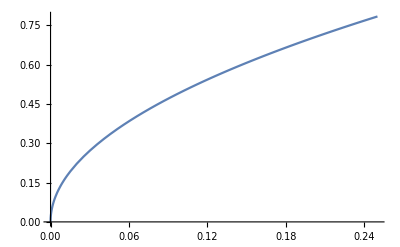

```mathematica
Plot[(2*2 ⅈ √g2 √h1 √ω)/(√(β^2+ω^2) √(h3 (-(12 q)/ω+(144 g0 ω^3)/(β^4+5 β^2 ω^2+4 ω^4))))/.h1->0.212511000656/.h3->-0.212511000656/6/.ω-> 1.42411271695/.β->1/.q->.5/.g0-> 1.5,{g2,0,.25}]
```

ignore everything below this point.

```mathematica
FullSimplify[h3 (-(12 q)/ω+(144 g0 ω^3)/(β^4+5 β^2 ω^2+4 ω^4))(β^4+5 β^2 ω^2+4 ω^4)ω]
```

-12 h3 (-12 g0 ω^4+q (β^2+ω^2) (β^2+4 ω^2))

```mathematica
FullSimplify[(2 ⅈ √g2 √h1 √ω)/(√(β^2+ω^2) √(-12 h3 (-12 g0 ω^4+q (β^2+ω^2) (β^2+4 ω^2))))Sqrt[ω (β^4+5 β^2 ω^2+4 ω^4)]]
```

(ⅈ √g2 √h1 √ω √(ω (β^2+ω^2) (β^2+4 ω^2)))/(√3 √(β^2+ω^2) √(-h3 (q β^4+5 q β^2 ω^2+4 (-3 g0+q) ω^4)))

```mathematica
(2 √h1 √ω)/(√(β^2+ω^2) √(h3 ((12 q)/ω-(144 g0 ω^3)/(β^4+5 β^2 ω^2+4 ω^4))))
```